```mathematica
SetDirectory[""];
```

SetDirectory::badfile: 指定の引数は有効な文字列かFileでなければなりません．

```mathematica
(*節点のx座標リスト*)
tlist={1,2,3,4,5};
```

## Bスプライン関数0次から3次まで作成

```mathematica
(*０次を定義*)
```

```mathematica
b0[x_,j_]:=1/;tlist[[j]]≤x≤tlist[[j+1]];
b0[x_,j_]:=0/;tlist[[j]]>x ;
b0[x_,j_]:=0/;x>tlist[[j+1]];
```

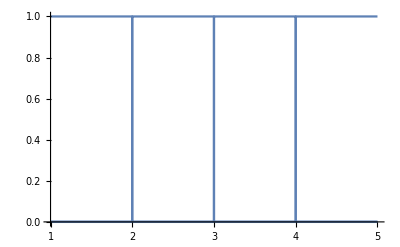

```mathematica
Show[Table[Plot[b0[x,j],{x,1,5}],{j,1,4}]]
```

```mathematica
(*一次を漸化式で求める*)
```

```mathematica
b1[x_,j_]:=(x-tlist[[j]])/(tlist[[j+1]]-tlist[[j]])b0[x,j]+(tlist[[j+2]]-x)/(tlist[[j+2]]-tlist[[j+1]])b0[x,j+1]
```

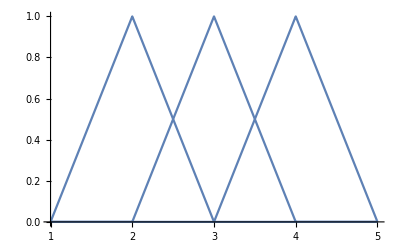

```mathematica
Show[Table[Plot[b1[x,j],{x,1,5}],{j,1,3}]]
```

```mathematica
(*二次*)
```

```mathematica
b2[x_,j_]:=(x-tlist[[j]])/(tlist[[j+2]]-tlist[[j]])b1[x,j]+(tlist[[j+3]]-x)/(tlist[[j+3]]-tlist[[j+1]])b1[x,j+1]
```

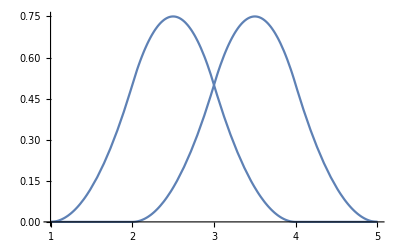

```mathematica
Show[Table[Plot[b2[x,j],{x,1,5}],{j,1,2}]]
```

```mathematica
(*三次の完成*)
```

```mathematica
b3[x_,j_]:=(x-tlist[[j]])/(tlist[[j+3]]-tlist[[j]])b2[x,j]+(tlist[[j+4]]-x)/(tlist[[j+4]]-tlist[[j+1]])b2[x,j+1]
```

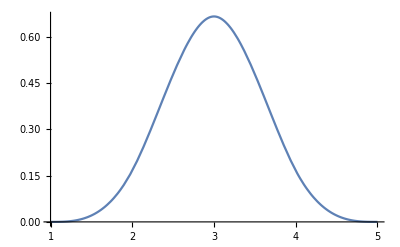

```mathematica
Plot[b3[x,1],{x,1,5}]
```

## 簡単な例で3次Bスプラインフィッティング(失敗例)

```mathematica
(*Bスプライン関数を節点の任意の間隔で作るように一般化*)
```

```mathematica
b0[tlist_,x_,j_]:=1/;tlist[[j]]≤x≤tlist[[j+1]];
b0[tlist_,x_,j_]:=0/;tlist[[j]]>x ;
b0[tlist_,x_,j_]:=0/;x>tlist[[j+1]];
b1[tlist_,x_,j_]:=(x-tlist[[j]])/(tlist[[j+1]]-tlist[[j]])b0[tlist,x,j]+(tlist[[j+2]]-x)/(tlist[[j+2]]-tlist[[j+1]])b0[tlist,x,j+1];
b2[tlist_,x_,j_]:=(x-tlist[[j]])/(tlist[[j+2]]-tlist[[j]])b1[tlist,x,j]+(tlist[[j+3]]-x)/(tlist[[j+3]]-tlist[[j+1]])b1[tlist,x,j+1];
b3[tlist_,x_,j_]:=(x-tlist[[j]])/(tlist[[j+3]]-tlist[[j]])b2[tlist,x,j]+(tlist[[j+4]]-x)/(tlist[[j+4]]-tlist[[j+1]])b2[tlist,x,j+1]
```

```mathematica
(*節点のリスト*)
list={0,1.1,2.5,4.2,5,7,8,9,10,12};
(*5点ずつに分ける*)
tsublist=Table[list[[i;;i+4]],{i,1,Length[list]-4}]
```

{{0,1.1,2.5,4.2,5},{1.1,2.5,4.2,5,7},{2.5,4.2,5,7,8},{4.2,5,7,8,9},{5,7,8,9,10},{7,8,9,10,12}}

```mathematica
(*区間の長さがそれぞれ微妙に違ってもBスプラインを簡単に作れる*)
```

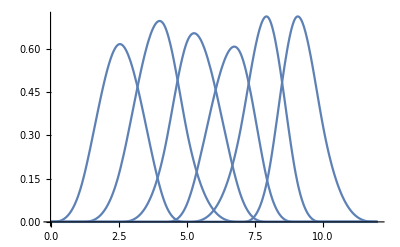

```mathematica
Show[Table[Plot[b3[tsublist[[k]],x,1],{x,tsublist[[1]][[1]],tsublist[[-1]][[-1]]}],{k,1,Length[tsublist]}],PlotRange->All]
```

```mathematica
(*適当な散布図を用意*)
```

```mathematica
points={{0,0},{1,1},{2,3},{3,7},{4,4},{5,5}};
```

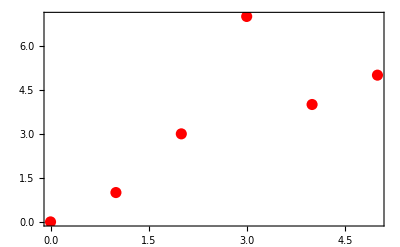

```mathematica
p0=ListPlot[points,PlotStyle->{Red,PointSize[0.02]},Frame->True]
```

```mathematica
(*6点のデータ点、区間は5分割した時のフィッティング*)
(*スプライン関数を2つとしてやっちゃった例*)
```

```mathematica
(*n分割した節点を求める関数*)
parting[points_,n_]:=Module[{points2},
points2=Sort[points,#1[[1]]<#2[[1]]&];
Range[points2[[1]][[1]],points2[[-1]][[1]],(points2[[-1]][[1]]-points2[[1]][[1]])/n]]
```

```mathematica
parting[points,5]
```

{0,1,2,3,4,5}

```mathematica
tsublist2=Table[points[[;;,1]][[i;;i+4]],{i,1,Length[points]-4}]
```

{{0,1,2,3,4},{1,2,3,4,5}}

```mathematica
(*愚直に各スプラインにω1,ω2をかけて、各データ点での値を求める*)
```

```mathematica
xv=(Table[b3[tsublist2[[k]],#,1]&/@points[[;;,1]],{k,1,2}]*{ω1,ω2})
```

{{0,ω1/3,(4 ω1)/3,ω1/3,0,0},{0,0,ω2/3,(4 ω2)/3,ω2/3,0}}

```mathematica
(*残差の二乗和の算出。回りくどい*)
```

```mathematica
e=(points[[;;,2]]-xv[[1]]-xv[[2]])^2//Total
```

25+(1-ω1/3)^2+(7-ω1/3-(4 ω2)/3)^2+(4-ω2/3)^2+(3-(4 ω1)/3-ω2/3)^2

```mathematica
sol=FindMinimum[e,{ω1,ω2}]
```

{30.5769,{ω1→0.923077,ω2→5.42308}}

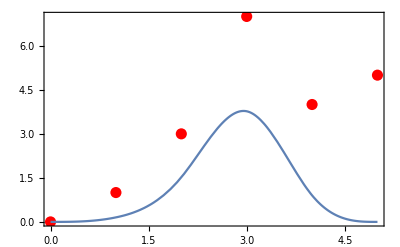

```mathematica
p=b3[tsublist2[[1]],x,1]*ω1+b3[tsublist2[[2]],x,1]*ω2/.sol[[2]];
Show[p0,Plot[p,{x,0,5},PlotRange->All]/.sol[[2]]]
```

```mathematica
(*ここで過ちに気づく*)
```

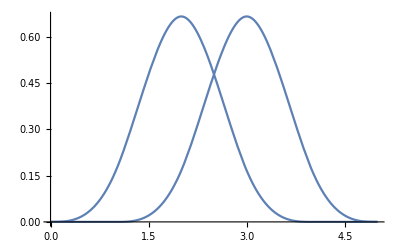

```mathematica
Plot[Table[b3[tsublist2[[k]],x,1],{k,1,2}],{x,0,5}]
```

## 正しい基底関数の個数でのフィッティング

```mathematica
(*左右に節点を３つずつ増やした節点のリストを作成*)
```

```mathematica
partex[points_,n_]:=Module[{points2,dx},
points2=Sort[points,#1[[1]]<#2[[1]]&];
dx=(points2[[-1]][[1]]-points2[[1]][[1]])/n;
Range[points2[[1]][[1]]-3dx,points2[[-1]][[1]]+3dx,dx]]
```

```mathematica
points2=Sort[{{0,0},{1,1},{2,3},{3,1},{4,4},{5,5},{1.4,3.3},{2.3,2},{0.4,1.5}},#1[[1]]<#2[[1]]&];
```

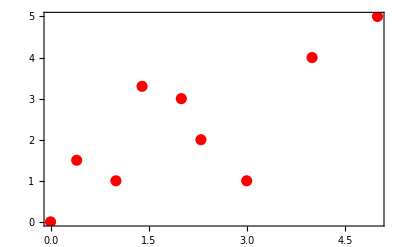

```mathematica
p2=ListPlot[points2,PlotStyle->{Red,PointSize[0.02]},Frame->True]
```

```mathematica
pe=partex[points2,4]
```

{-15/4,-5/2,-5/4,0,5/4,5/2,15/4,5,25/4,15/2,35/4}

```mathematica
(*5点ずつの節点のリストを作成*)
```

```mathematica
tsublist3=Table[pe[[i;;i+4]],{i,1,Length[pe]-4}]
```

{{-15/4,-5/2,-5/4,0,5/4},{-5/2,-5/4,0,5/4,5/2},{-5/4,0,5/4,5/2,15/4},{0,5/4,5/2,15/4,5},{5/4,5/2,15/4,5,25/4},{5/2,15/4,5,25/4,15/2},{15/4,5,25/4,15/2,35/4}}

```mathematica
(*正しい数の基底関数指さし確認ヨシ！*)
```

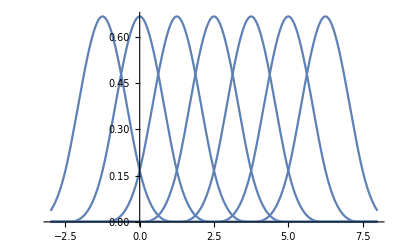

```mathematica
Plot[Table[b3[tsublist3[[k]],x,1],{k,1,Length[pe]-4}],{x,-3,8},PlotRange->All]
```

```mathematica
(*重みパラメータ一括作成。基底関数の数と同じ*)
```

```mathematica
ωlist=Subscript[ω,#]&/@Range[Length[pe]-4]
```

{ω_1,ω_2,ω_3,ω_4,ω_5,ω_6,ω_7}

```mathematica
(*各データ点のx座標での推定値*)
```

```mathematica
xv3=Total[Table[b3[tsublist3[[k]],#,1],{k,1,Length[pe]-4}]*ωlist]&/@points2[[;;,1]]
```

{ω_1/3+(4 ω_2)/3+ω_3/3,0.+0.0524053 ω_1+0.580651 ω_2+0.361483 ω_3+0.00546133 ω_4,ω_1/750+(106 ω_2)/375+(473 ω_3)/750+(32 ω_4)/375,0.+0.113579 ω_2+0.653131 ω_3+0.233003 ω_4+0.000288 ω_5,(4 ω_2)/375+(311 ω_3)/750+(202 ω_4)/375+(9 ω_5)/250,0.+0.000682667 ω_2+0.257419 ω_3+0.643115 ω_4+0.098784 ω_5,(9 ω_3)/250+(202 ω_4)/375+(311 ω_5)/750+(4 ω_6)/375,(32 ω_4)/375+(473 ω_5)/750+(106 ω_6)/375+ω_7/750,ω_5/3+(4 ω_6)/3+ω_7/3}

```mathematica
(*残差の二乗和*)
```

```mathematica
e3=(points2[[;;,2]]-xv3)^2//Total;
```

```mathematica
sol3=FindMinimum[e3,ωlist]
```

{2.27355,{ω_1→-3.11657,ω_2→0.143768,ω_3→2.79031,ω_4→3.06479,ω_5→-2.5092,ω_6→19.1137,ω_7→-58.9458}}

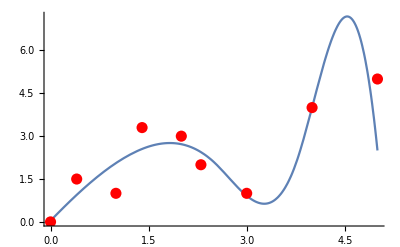

```mathematica
p3=Total[Table[b3[tsublist3[[k]],x,1],{k,1,Length[pe]-4}]*ωlist]/.sol3[[2]];
Show[Plot[p3,{x,0,5},PlotRange->All]/.sol3[[2]],p2]
```

```mathematica
(*データ点の座標のリストと分割数を与えるとフィッティングしてくれる関数*)
```

```mathematica
bspfit[points_,n_]:=Module[{tsublist3,ωlist,xv3,e3,sol3,p3,p0},
tsublist3=Table[partex[points,n][[i;;i+4]],{i,1,Length[partex[points,n]]-4}];
ωlist=Subscript[ω,#]&/@Range[Length[partex[points,n]]-4];
xv3=Total[Table[b3[tsublist3[[k]],#,1],{k,1,Length[partex[points,n]]-4}]*ωlist]&/@points[[;;,1]];
e3=(points[[;;,2]]-xv3)^2//Total;
sol3=FindMinimum[e3,ωlist];
p0=ListPlot[points,PlotStyle->{Red,PointSize[0.02]},Frame->True,AspectRatio->1,Axes->False];
p3=Total[Table[b3[tsublist3[[k]],x,1],{k,1,Length[partex[points,n]]-4}]*ωlist]/.sol3[[2]];
Show[p0,Plot[p3,{x,Min[points[[;;,1]]]-2,Max[points[[;;,1]]]+2},PlotRange->All]/.sol3[[2]]]
]
```

```mathematica
(*細かく区切りすぎると挙動が不安定に*)
```

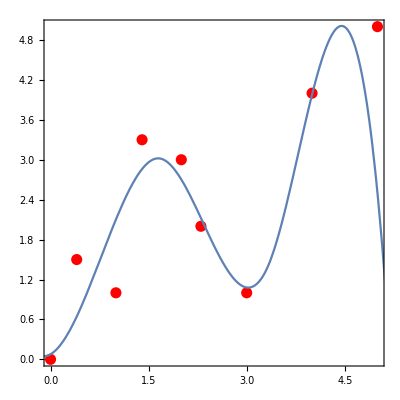

```mathematica
bspfit[points2,3]
```

```mathematica
data=Import["motercycle-impact-data.csv"];
```

```mathematica
time=data[[;;,1]];(*ms*)
accel=data[[;;,2]];(*G*)
```

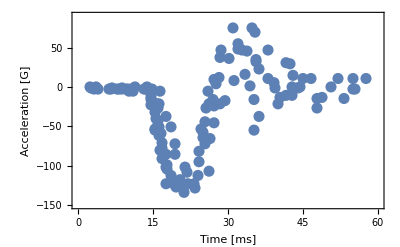

```mathematica
p0 =ListPlot[Transpose[{time, accel}],Frame->True,
PlotStyle->PointSize[0.02],
PlotRange->{{0,60},{-150,90}},
Axes->None,
FrameLabel->{Style["Time [ms]",Black,16],Style["Acceleration [G]",Black,16]}]
```

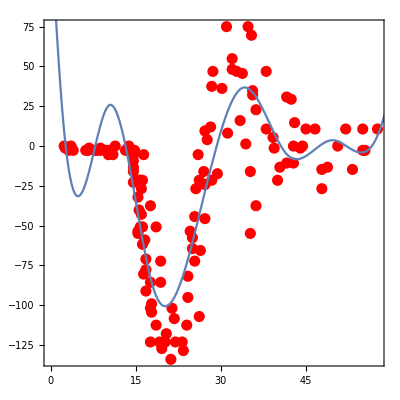

```mathematica
bspfit[data,7](*基底関数10個*)
```

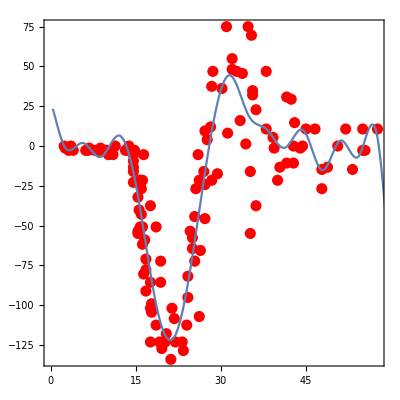

```mathematica
bspfit[data,17](*基底関数20個*)
```

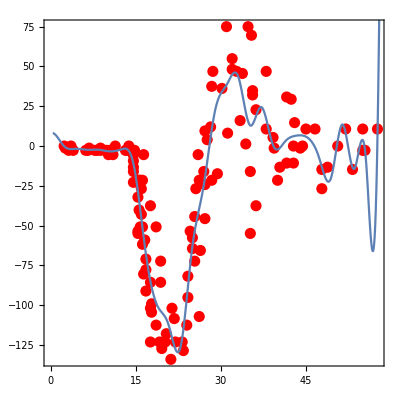

```mathematica
bspfit[data,27](*基底関数30個*)
```

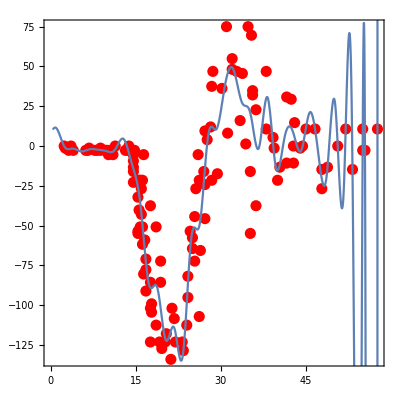

```mathematica
bspfit[data,37](*基底関数40個*)
```

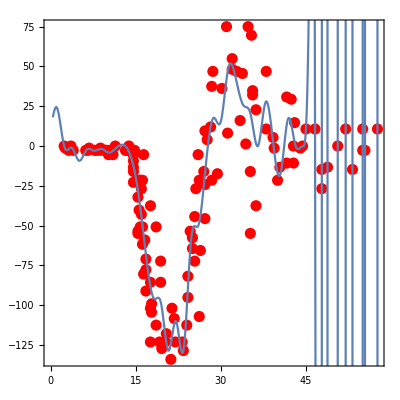

```mathematica
bspfit[data,42](*基底関数45個,後ろの方が計算できず*)
```